InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>]

InterpolatingFunction::dmval: Input value {60., 40.} lies outside the range of data in the interpolating function. Extrapolation will be used.

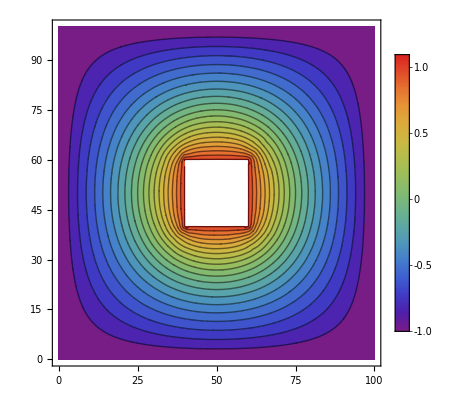

```mathematica
Ω=RegionDifference[Rectangle[{0,0},{100,100}],Rectangle[{40,40},{60,60}]];
sol=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==0,DirichletCondition[u[x,y]==1.,x==40&&40≤y≤60||x==60&&40≤y≤60||40≤x≤60&&y==40||40≤x≤60&&y==60],u[x,0]==u[x,100]==u[0,y]==u[100,y]==-1},u,{x,y}∈Ω]

ContourPlot[sol[x,y],{x,y}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic,PlotPoints->50,Contours->20]
```

```mathematica
D[sol[x,y],x]
```

InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>][x,y]

```mathematica
?StreamPlot
```

StreamPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}] generates a stream plot of the vector field {v_x,v_y} as a function of x and y. 
StreamPlot[{{v_x,v_y},{w_x,w_y},…},{x,x_min,x_max},{y,y_min,y_max}] generates plots of several vector fields.

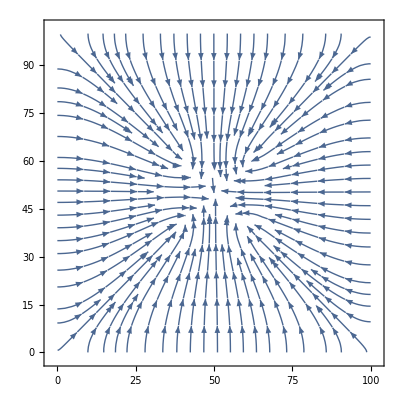

```mathematica
StreamPlot[Evaluate[{D[sol[x,y],x],D[sol[x,y],y]}],{x,0,100},{y,0,100}]
```

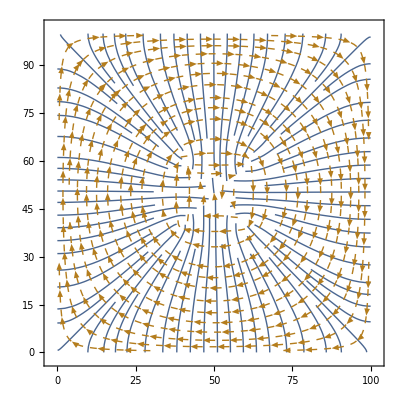

```mathematica
StreamPlot[Evaluate[{D[sol[x,y],x],D[sol[x,y],y]} /. {A_,B_}->{{A,B},{-B,A}} ],{x,0,100},{y,0,100},StreamStyle->{"Line",{"Line",Directive[Dashed]}}]
```

```mathematica
?StreamPlot
```

StreamPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}] generates a stream plot of the vector field {v_x,v_y} as a function of x and y. 
StreamPlot[{{v_x,v_y},{w_x,w_y},…},{x,x_min,x_max},{y,y_min,y_max}] generates plots of several vector fields.

```mathematica
Options[StreamPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ColorFunction→None,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→Automatic,MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotRange→{Full,Full},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,StreamColorFunction→None,StreamColorFunctionScaling→True,StreamPoints→Automatic,StreamScale→Automatic,StreamStyle→Automatic,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},VectorColorFunction→None,VectorColorFunctionScaling→True,VectorPoints→None,VectorScale→Automatic,VectorStyle→Automatic,WorkingPrecision→MachinePrecision}

```mathematica
NDSolveValue[{∇_{x,y}^2 u[x,y]==0,DirichletCondition[u[x,y]==0,x≥2  && y≥2 || x≤0 && y≤0],DirichletCondition[u[x,y]==1,1≤x<1.5 && 1≤y≤1.5]},u,{x,y}∈Rectangle[{0,0},{2,2}]]
```

NDSolveValue::bcnop: No places were found on the boundary where 1 ≤ x < 1.5 && 1 ≤ y ≤ 1.5 was True, so DirichletCondition[u == 1, 1 ≤ x < 1.5 && 1 ≤ y ≤ 1.5] will effectively be ignored.

InterpolatingFunction[{{0., 2.}, {0., 2.}}, <>]

```mathematica
Dom=Rectangle[{-100,-100},{100,100}]
```

Rectangle[{-100,-100},{100,100}]

```mathematica
strip = Rectangle[{-5,-0.5},{5,0.5}]
```

Rectangle[{-5,-0.5},{5,0.5}]

```mathematica
base=Rectangle[{-50,-10},{50,10}]
```

Rectangle[{-50,-10},{50,10}]

```mathematica
Ω=RegionDifference[Dom,base];
```

```mathematica
DCbool[Rectangle[A_,B_]]:= ((x==A[[1]] || x==B[[1]] ) && (y==A[[2]] || y==B[[2]]))
```

```mathematica
DirichletCondition[u[x,y]==1,DCbool[base]]
```

DirichletCondition[u[x,y]==1,(x==-50||x==50)&&(y==-10||y==10)]

InterpolatingFunction[{{-100., 100.}, {-100., 100.}}, <>]

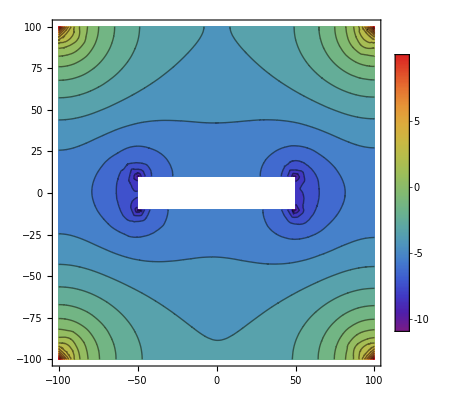

```mathematica
sol=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==0,DirichletCondition[u[x,y]==10,DCbool[Dom]],DirichletCondition[u[x,y]==-10,DCbool[base]]},u,{x,y}∈Ω]

ContourPlot[sol[x,y],{x,y}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic,PlotPoints->50,Contours->20]
```

```mathematica
Plot3D[%[x,y],{x,y}∈Rectangle[{0,0},{2,2}]]
```

-Graphics3D-